1 - 9 General solution
Find a real general solution of the following systems.

1.  y_1'=y_1+y_2
y_2'=3 y_1-y_2

```mathematica
ClearAll["Global`*"]
```

Mathematica solves the system, but to knock the solutions into a framework which can be directly compared with the text answer, some wrangling, rearranging, and substituting must be done.

```mathematica
rit={y1'[t]==y1[t]+y2[t],y2'[t]==3 y1[t]-y2[t]}
git=DSolve[rit,{y1,y2},t]
```

{y1'[t]==y1[t]+y2[t],y2'[t]==3 y1[t]-y2[t]}

{{y1→Function[{t},1/4 ⅇ^(-2 t) (1+3 ⅇ^(4 t)) C[1]+1/4 ⅇ^(-2 t) (-1+ⅇ^(4 t)) C[2]],y2→Function[{t},3/4 ⅇ^(-2 t) (-1+ⅇ^(4 t)) C[1]+1/4 ⅇ^(-2 t) (3+ⅇ^(4 t)) C[2]]}}

```mathematica
fit=Expand[git[[1,1,2,2]]]
```

1/4 ⅇ^(-2 t) C[1]+3/4 ⅇ^(2 t) C[1]-1/4 ⅇ^(-2 t) C[2]+1/4 ⅇ^(2 t) C[2]

```mathematica
vit=Expand[4 fit]
```

ⅇ^(-2 t) C[1]+3 ⅇ^(2 t) C[1]-ⅇ^(-2 t) C[2]+ⅇ^(2 t) C[2]

```mathematica
bit=Collect[vit,ⅇ^(-2 t)]
```

ⅇ^(-2 t) (C[1]-C[2])+ⅇ^(2 t) (3 C[1]+C[2])

Having reconciled the form of the constants of integration, a recognizable variant emerges.

```mathematica
mit=bit/.{(C[1]-C[2])->c1,(3 C[1]+C[2])->c2}
```

c1 ⅇ^(-2 t)+c2 ⅇ^(2 t)

```mathematica
wit=Expand[git[[1,2,2,2]]]
```

-3/4 ⅇ^(-2 t) C[1]+3/4 ⅇ^(2 t) C[1]+3/4 ⅇ^(-2 t) C[2]+1/4 ⅇ^(2 t) C[2]

```mathematica
pit=Expand[4 wit]
```

-3 ⅇ^(-2 t) C[1]+3 ⅇ^(2 t) C[1]+3 ⅇ^(-2 t) C[2]+ⅇ^(2 t) C[2]

```mathematica
sit=Collect[pit,ⅇ^(-2 t)]
```

ⅇ^(2 t) (3 C[1]+C[2])+ⅇ^(-2 t) (-3 C[1]+3 C[2])

```mathematica
kit=sit/.(-3 C[1]+3 C[2])->(-3 (C[1]-C[2]))
```

-3 ⅇ^(-2 t) (C[1]-C[2])+ⅇ^(2 t) (3 C[1]+C[2])

```mathematica
lit=kit/.{(C[1]-C[2])->c1,(3 C[1]+C[2])->c2}
```

-3 c1 ⅇ^(-2 t)+c2 ⅇ^(2 t)

1. Above: The top green cell ‘mit’ is y1, the bottom green cell ‘lit’ is y2. They both match the text expressions, even to the constants. Care was taken to make sure equal constant substitutions were made in both cases (yellow).

3.  y_1'=y_1+2 y_2
y_2'=y_1+2 y_2

```mathematica
ClearAll["Global`*"]
```

```mathematica
nar={y1'[t]==y1[t]+ 2 y2[t],y2'[t]==1/2 y1[t]+y2[t]}
bar=DSolve[nar,{y1,y2},t]
```

{y1'[t]==y1[t]+2 y2[t],y2'[t]==y1[t]/2+y2[t]}

{{y1→Function[{t},1/2 (1+ⅇ^(2 t)) C[1]+(-1+ⅇ^(2 t)) C[2]],y2→Function[{t},1/4 (-1+ⅇ^(2 t)) C[1]+1/2 (1+ⅇ^(2 t)) C[2]]}}

```mathematica
mar=Expand[bar[[1,1,2,2]]]
```

C[1]/2+1/2 ⅇ^(2 t) C[1]-C[2]+ⅇ^(2 t) C[2]

```mathematica
uar=Expand[2mar]
```

C[1]+ⅇ^(2 t) C[1]-2 C[2]+2 ⅇ^(2 t) C[2]

```mathematica
sar=uar/.( C[1]-2 C[2])->( c2)
```

c2+ⅇ^(2 t) C[1]+2 ⅇ^(2 t) C[2]

```mathematica
tar=Collect[sar,ⅇ^(2 t)]
```

c2+ⅇ^(2 t) (C[1]+2 C[2])

```mathematica
var=tar/.(C[1]+2 C[2])->c1
```

c2+c1 ⅇ^(2 t)

```mathematica
jar=Expand[2 var]
```

2 c2+2 c1 ⅇ^(2 t)

```mathematica
par=Expand[bar[[1,2,2,2]]]
```

-C[1]/4+1/4 ⅇ^(2 t) C[1]+C[2]/2+1/2 ⅇ^(2 t) C[2]

```mathematica
har=Expand[4 par]
```

-C[1]+ⅇ^(2 t) C[1]+2 C[2]+2 ⅇ^(2 t) C[2]

```mathematica
dar=har/.( -C[1]+2 C[2])->(- c2)
```

-c2+ⅇ^(2 t) C[1]+2 ⅇ^(2 t) C[2]

```mathematica
qar=Collect[dar,ⅇ^(2 t)]
```

-c2+ⅇ^(2 t) (C[1]+2 C[2])

```mathematica
xar=qar/.(C[1]+2 C[2])->c1
```

-c2+c1 ⅇ^(2 t)

1. Above: The functions ‘jar’ and ‘xar’, (upper and lower green cells respectively), are y1 and y2, and match the text answer. Note that in assembling the functions, each was multiplied by 4. However, care was taken so that the proportions and signs of the constants match those of the text.

5.  y_1'=2 y_1+5 y_2
y_2'=5 y_1+12.5 y_2

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==2 y1[t]+5 y2[t],y2'[t]==5 y1[t]+12.5 y2[t]}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==2 y1[t]+5 y2[t],y2'[t]==5 y1[t]+12.5 y2[t]}

{{y1→Function[{t},0.137931 ⅇ^(-2.22045×10^-16 t) (6.25+1. ⅇ^(14.5 t)) C[1]+0.344828 ⅇ^(-2.22045×10^-16 t) (-1.+1. ⅇ^(14.5 t)) C[2]],y2→Function[{t},0.344828 ⅇ^(-2.22045×10^-16 t) (-1.+1. ⅇ^(14.5 t)) C[1]+0.862069 ⅇ^(-2.22045×10^-16 t) (0.16+1. ⅇ^(14.5 t)) C[2]]}}

```mathematica
e3=e2[[1,1,2,2]]
```

0.137931 ⅇ^(-2.22045×10^-16 t) (6.25+1. ⅇ^(14.5 t)) C[1]+0.344828 ⅇ^(-2.22045×10^-16 t) (-1.+1. ⅇ^(14.5 t)) C[2]

```mathematica
e16=e3/.{C[1]->C1,C[2]->C2}
```

0.344828 C2 ⅇ^(-2.22045×10^-16 t) (-1.+1. ⅇ^(14.5 t))+0.137931 C1 ⅇ^(-2.22045×10^-16 t) (6.25+1. ⅇ^(14.5 t))

```mathematica
e4=Chop[e16,10^-15]
```

0.344828 C2 (-1.+1. ⅇ^(14.5 t))+0.137931 C1 (6.25+1. ⅇ^(14.5 t))

```mathematica
e5=Expand[e4]
```

0.862069 C1-0.344828 C2+0.137931 C1 ⅇ^(14.5 t)+0.344828 C2 ⅇ^(14.5 t)

```mathematica
e6=Collect[e5,ⅇ^(14.5 t)]
```

0.862069 C1-0.344828 C2+(0.137931 C1+0.344828 C2) ⅇ^(14.5 t)

```mathematica
e7=e6/.(0.13793103448275862 C1+0.3448275862068965 C2)->2c2
```

0.862069 C1-0.344828 C2+2 c2 ⅇ^(14.5 t)

```mathematica
e8=e7/.(0.8620689655172413 C1-0.3448275862068966 C2)->5c1
```

5 c1+2 c2 ⅇ^(14.5 t)

```mathematica
Solve[0.13793103448275862 +0.3448275862068965 ==2c21,c21]
```

{{c21→0.241379}}

```mathematica
Solve[0.8620689655172413-0.3448275862068966==5 c11,c11]
```

{{c11→0.103448}}

```mathematica
e10=e2[[1,2,2,2]]
```

0.344828 ⅇ^(-2.22045×10^-16 t) (-1.+1. ⅇ^(14.5 t)) C[1]+0.862069 ⅇ^(-2.22045×10^-16 t) (0.16+1. ⅇ^(14.5 t)) C[2]

```mathematica
e17=e10/.{C[1]->C1,C[2]->C2}
```

0.344828 C1 ⅇ^(-2.22045×10^-16 t) (-1.+1. ⅇ^(14.5 t))+0.862069 C2 ⅇ^(-2.22045×10^-16 t) (0.16+1. ⅇ^(14.5 t))

```mathematica
e11=Chop[e17,10^-15]
```

0.344828 C1 (-1.+1. ⅇ^(14.5 t))+0.862069 C2 (0.16+1. ⅇ^(14.5 t))

```mathematica
e12=Expand[e11]
```

-0.344828 C1+0.137931 C2+0.344828 C1 ⅇ^(14.5 t)+0.862069 C2 ⅇ^(14.5 t)

```mathematica
e13=Collect[e12,ⅇ^(14.5 t)]
```

-0.344828 C1+0.137931 C2+(0.344828 C1+0.862069 C2) ⅇ^(14.5 t)

```mathematica
e14=e13/.(0.3448275862068966 C1+0.8620689655172414 C2)->5 c2
```

-0.344828 C1+0.137931 C2+5 c2 ⅇ^(14.5 t)

```mathematica
Solve[0.3448275862068966 +0.8620689655172414==5 c22,c22]
```

{{c22→0.241379}}

```mathematica
e15=e14/.(-0.3448275862068965 C1+0.13793103448275862 C2)->(-2 c1)
```

-2 c1+5 c2 ⅇ^(14.5 t)

```mathematica
Solve[-0.3448275862068965+0.13793103448275862==-2 c21,c21]
```

{{c21→0.103448}}

1. Above: y1 is given by e8; y2 is given by e15. These expressions match the text answers. Green cells are for function formulas, yellow cells for sites of assignment of values of constants, pink cells for constant value verification. The equality of c11,c12; and c21,c22 shows that due consideration was given to preserving the values and proportions of the constants. (In calculating the numerical value of constants for comparison, the values of Mathematica's constants was taken as all 1.)

7.  y_1'=y_2
y_2'=-y_1+y_3
y_3'=-y_2

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==y2[t],y2'[t]==-y1[t]+y3[t],y3'[t]==-y2[t]}
e2=DSolve[e1,{y1,y2,y3},t]
```

{y1'[t]==y2[t],y2'[t]==-y1[t]+y3[t],y3'[t]==-y2[t]}

{{y1→Function[{t},1/2 C[3] (1-Cos[√2 t])+1/2 C[1] (1+Cos[√2 t])+(C[2] Sin[√2 t])/(√2)],y2→Function[{t},C[2] Cos[√2 t]-(C[1] Sin[√2 t])/(√2)+(C[3] Sin[√2 t])/(√2)],y3→Function[{t},1/2 C[1] (1-Cos[√2 t])+1/2 C[3] (1+Cos[√2 t])-(C[2] Sin[√2 t])/(√2)]}}

```mathematica
e3=e2[[1,1,2,2]]
```

1/2 C[3] (1-Cos[√2 t])+1/2 C[1] (1+Cos[√2 t])+(C[2] Sin[√2 t])/(√2)

```mathematica
e4=Expand[ 2e3]
```

C[1]+C[3]+C[1] Cos[√2 t]-C[3] Cos[√2 t]+√2 C[2] Sin[√2 t]

```mathematica
e5=Collect[e4,Cos[√2 t]]
```

C[1]+C[3]+(C[1]-C[3]) Cos[√2 t]+√2 C[2] Sin[√2 t]

```mathematica
e6=e5/.(C[1]+C[3])->c1
```

c1+(C[1]-C[3]) Cos[√2 t]+√2 C[2] Sin[√2 t]

```mathematica
e7=e6/.(C[1]-C[3])->-c2
```

c1-c2 Cos[√2 t]+√2 C[2] Sin[√2 t]

```mathematica
e8=e7/.(√2 C[2])->c3
```

c1-c2 Cos[√2 t]+c3 Sin[√2 t]

```mathematica
e9=e2[[1,2,2,2]]
```

C[2] Cos[√2 t]-(C[1] Sin[√2 t])/(√2)+(C[3] Sin[√2 t])/(√2)

```mathematica
e10=Expand[2 e9]
```

2 C[2] Cos[√2 t]-√2 C[1] Sin[√2 t]+√2 C[3] Sin[√2 t]

```mathematica
e11=e10/.C[2]->c3/(√2)
```

√2 c3 Cos[√2 t]-√2 C[1] Sin[√2 t]+√2 C[3] Sin[√2 t]

```mathematica
e12=Collect[e11,√2 Sin[√2 t]]
```

√2 c3 Cos[√2 t]+√2 (-C[1]+C[3]) Sin[√2 t]

```mathematica
e13=e12/.(-C[1]+C[3])->c2
```

√2 c3 Cos[√2 t]+√2 c2 Sin[√2 t]

```mathematica
e14=e2[[1,3,2,2]]
```

1/2 C[1] (1-Cos[√2 t])+1/2 C[3] (1+Cos[√2 t])-(C[2] Sin[√2 t])/(√2)

```mathematica
e15=Expand[2 e14]
```

C[1]+C[3]-C[1] Cos[√2 t]+C[3] Cos[√2 t]-√2 C[2] Sin[√2 t]

```mathematica
e16=e15/.(C[1]+C[3])->c1
```

c1-C[1] Cos[√2 t]+C[3] Cos[√2 t]-√2 C[2] Sin[√2 t]

```mathematica
e17=Collect[e16,Cos[√2 t]]
```

c1+(-C[1]+C[3]) Cos[√2 t]-√2 C[2] Sin[√2 t]

```mathematica
e18=e17/.(-C[1]+C[3])->c2
```

c1+c2 Cos[√2 t]-√2 C[2] Sin[√2 t]

```mathematica
e19=e18/.(√2 C[2])->c3
```

c1+c2 Cos[√2 t]-c3 Sin[√2 t]

1. Above: The function forms for y1,y2,and y3 match the green cells above in order, conforming to the text function forms. The system of symbolic constant conversion established for y1 was carried forward and used for the remaining two functions. It was found that this system matched the text symbolic constant assignments exactly. Each function was upscaled by 2 during assembly.

9.  y_1'=10 y_1-10 y_2-4 y_3
y_2'=-10 y_1+y_2-14 y_3
y_3'=-4 y_1-14 y_2-2 y_3

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==10 y1[t]-10 y2[t]-4 y3[t],y2'[t]==-10 y1[t]+y2[t]-14 y3[t],y3'[t]==-4 y1[t]-14 y2[t]-2 y3[t]}
e2=DSolve[e1,{y1,y2,y3},t]
```

{y1'[t]==10 y1[t]-10 y2[t]-4 y3[t],y2'[t]==-10 y1[t]+y2[t]-14 y3[t],y3'[t]==-4 y1[t]-14 y2[t]-2 y3[t]}

{{y1→Function[{t},1/9 ⅇ^(-18 t) (1+4 ⅇ^(27 t)+4 ⅇ^(36 t)) C[1]-2/9 ⅇ^(-18 t) (-1-ⅇ^(27 t)+2 ⅇ^(36 t)) C[2]+2/9 ⅇ^(-18 t) (1-2 ⅇ^(27 t)+ⅇ^(36 t)) C[3]],y2→Function[{t},-2/9 ⅇ^(-18 t) (-1-ⅇ^(27 t)+2 ⅇ^(36 t)) C[1]+1/9 ⅇ^(-18 t) (4+ⅇ^(27 t)+4 ⅇ^(36 t)) C[2]-2/9 ⅇ^(-18 t) (-2+ⅇ^(27 t)+ⅇ^(36 t)) C[3]],y3→Function[{t},2/9 ⅇ^(-18 t) (1-2 ⅇ^(27 t)+ⅇ^(36 t)) C[1]-2/9 ⅇ^(-18 t) (-2+ⅇ^(27 t)+ⅇ^(36 t)) C[2]+1/9 ⅇ^(-18 t) (4+4 ⅇ^(27 t)+ⅇ^(36 t)) C[3]]}}

```mathematica
e3=e2[[1,1,2,2]]
```

1/9 ⅇ^(-18 t) (1+4 ⅇ^(27 t)+4 ⅇ^(36 t)) C[1]-2/9 ⅇ^(-18 t) (-1-ⅇ^(27 t)+2 ⅇ^(36 t)) C[2]+2/9 ⅇ^(-18 t) (1-2 ⅇ^(27 t)+ⅇ^(36 t)) C[3]

```mathematica
Expand[e3]
```

1/9 ⅇ^(-18 t) C[1]+4/9 ⅇ^(9 t) C[1]+4/9 ⅇ^(18 t) C[1]+2/9 ⅇ^(-18 t) C[2]+2/9 ⅇ^(9 t) C[2]-4/9 ⅇ^(18 t) C[2]+2/9 ⅇ^(-18 t) C[3]-4/9 ⅇ^(9 t) C[3]+2/9 ⅇ^(18 t) C[3]

```mathematica
e4=Expand[9 e3]
```

ⅇ^(-18 t) C[1]+4 ⅇ^(9 t) C[1]+4 ⅇ^(18 t) C[1]+2 ⅇ^(-18 t) C[2]+2 ⅇ^(9 t) C[2]-4 ⅇ^(18 t) C[2]+2 ⅇ^(-18 t) C[3]-4 ⅇ^(9 t) C[3]+2 ⅇ^(18 t) C[3]

```mathematica
e5=Collect[e4,ⅇ^(-18 t)]
```

ⅇ^(9 t) (4 C[1]+2 C[2]-4 C[3])+ⅇ^(18 t) (4 C[1]-4 C[2]+2 C[3])+ⅇ^(-18 t) (C[1]+2 C[2]+2 C[3])

```mathematica
e6=e5/.(C[1]+2 C[2]+2 C[3])->1/2 c1
```

1/2 c1 ⅇ^(-18 t)+ⅇ^(9 t) (4 C[1]+2 C[2]-4 C[3])+ⅇ^(18 t) (4 C[1]-4 C[2]+2 C[3])

```mathematica
e7=e6/.(4 C[1]+2 C[2]-4 C[3])->2 c2
```

1/2 c1 ⅇ^(-18 t)+2 c2 ⅇ^(9 t)+ⅇ^(18 t) (4 C[1]-4 C[2]+2 C[3])

```mathematica
e8=e7/.(4 C[1]-4 C[2]+2 C[3])->-c3
```

1/2 c1 ⅇ^(-18 t)+2 c2 ⅇ^(9 t)-c3 ⅇ^(18 t)

```mathematica
e9=e2[[1,2,2,2]]
```

-2/9 ⅇ^(-18 t) (-1-ⅇ^(27 t)+2 ⅇ^(36 t)) C[1]+1/9 ⅇ^(-18 t) (4+ⅇ^(27 t)+4 ⅇ^(36 t)) C[2]-2/9 ⅇ^(-18 t) (-2+ⅇ^(27 t)+ⅇ^(36 t)) C[3]

```mathematica
e10=Expand[9 e9]
```

2 ⅇ^(-18 t) C[1]+2 ⅇ^(9 t) C[1]-4 ⅇ^(18 t) C[1]+4 ⅇ^(-18 t) C[2]+ⅇ^(9 t) C[2]+4 ⅇ^(18 t) C[2]+4 ⅇ^(-18 t) C[3]-2 ⅇ^(9 t) C[3]-2 ⅇ^(18 t) C[3]

```mathematica
e11=Collect[e10,ⅇ^(-18 t)]
```

ⅇ^(9 t) (2 C[1]+C[2]-2 C[3])+ⅇ^(18 t) (-4 C[1]+4 C[2]-2 C[3])+ⅇ^(-18 t) (2 C[1]+4 C[2]+4 C[3])

```mathematica
e12=e11/.(2 C[1]+C[2]-2 C[3])->c2
```

c2 ⅇ^(9 t)+ⅇ^(18 t) (-4 C[1]+4 C[2]-2 C[3])+ⅇ^(-18 t) (2 C[1]+4 C[2]+4 C[3])

```mathematica
e13=e12/.(-4 C[1]+4 C[2]-2 C[3])->c3
```

c2 ⅇ^(9 t)+c3 ⅇ^(18 t)+ⅇ^(-18 t) (2 C[1]+4 C[2]+4 C[3])

```mathematica
e14=e13/.(2 C[1]+4 C[2]+4 C[3])->c1
```

c1 ⅇ^(-18 t)+c2 ⅇ^(9 t)+c3 ⅇ^(18 t)

```mathematica
e15=e2[[1,2,2,2]]
```

-2/9 ⅇ^(-18 t) (-1-ⅇ^(27 t)+2 ⅇ^(36 t)) C[1]+1/9 ⅇ^(-18 t) (4+ⅇ^(27 t)+4 ⅇ^(36 t)) C[2]-2/9 ⅇ^(-18 t) (-2+ⅇ^(27 t)+ⅇ^(36 t)) C[3]

```mathematica
e16=Expand[9 e15]
```

2 ⅇ^(-18 t) C[1]+2 ⅇ^(9 t) C[1]-4 ⅇ^(18 t) C[1]+4 ⅇ^(-18 t) C[2]+ⅇ^(9 t) C[2]+4 ⅇ^(18 t) C[2]+4 ⅇ^(-18 t) C[3]-2 ⅇ^(9 t) C[3]-2 ⅇ^(18 t) C[3]

```mathematica
e17=Collect[e16,ⅇ^(-18 t)]
```

ⅇ^(9 t) (2 C[1]+C[2]-2 C[3])+ⅇ^(18 t) (-4 C[1]+4 C[2]-2 C[3])+ⅇ^(-18 t) (2 C[1]+4 C[2]+4 C[3])

```mathematica
e18=e17/.(2 C[1]+C[2]-2 C[3])->-2 c2
```

-2 c2 ⅇ^(9 t)+ⅇ^(18 t) (-4 C[1]+4 C[2]-2 C[3])+ⅇ^(-18 t) (2 C[1]+4 C[2]+4 C[3])

```mathematica
e19=e18/.(-4 C[1]+4 C[2]-2 C[3])->-1/2 c3
```

-2 c2 ⅇ^(9 t)-1/2 c3 ⅇ^(18 t)+ⅇ^(-18 t) (2 C[1]+4 C[2]+4 C[3])

```mathematica
e20=e19/.(2 C[1]+4 C[2]+4 C[3])->c1
```

c1 ⅇ^(-18 t)-2 c2 ⅇ^(9 t)-1/2 c3 ⅇ^(18 t)

```mathematica
Solve[(2 C[1]+4 C[2]+4 C[3])==c1&&(-4 C[1]+4 C[2]-2 C[3])==-1/2 c3&&(2 C[1]+C[2]-2 C[3])==-2 c2,{c1,c2,c3}]
```

{{c1→2 (C[1]+2 C[2]+2 C[3]),c2→1/2 (-2 C[1]-C[2]+2 C[3]),c3→4 (2 C[1]-2 C[2]+C[3])}}

```mathematica
Solve[(2 C[1]+4 C[2]+4 C[3])==c1&&(-4 C[1]+4 C[2]-2 C[3])==c3&&(2 C[1]+C[2]-2 C[3])==c2,{c1,c2,c3}]
```

{{c1→2 (C[1]+2 C[2]+2 C[3]),c2→2 C[1]+C[2]-2 C[3],c3→-2 (2 C[1]-2 C[2]+C[3])}}

```mathematica
Solve[(4 C[1]-4 C[2]+2 C[3])==-c3&&(4 C[1]+2 C[2]-4 C[3])==2 c2&&(C[1]+2 C[2]+2 C[3])==1/2 c1,{c1,c2,c3}]
```

{{c1→2 (C[1]+2 C[2]+2 C[3]),c2→2 C[1]+C[2]-2 C[3],c3→-2 (2 C[1]-2 C[2]+C[3])}}

1. Above: Referring to green cells top to bottom, the function expressions match those of the text, y1, y2, y3, respectively. The constant coefficients were substituted as required to match those of the text; the three Solve jobs just above (pink cells) verify the coefficient assignment system as consistent and equivalent to the text.

10 - 15 IVPs
Solve the following initial value problems.

11.  y_1'=2 y_1+5 y_2
y_2'=-1/2 y_1-3/2 y_2
y_1[0]=-12, y_2[0]=0

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==2 y1[t]+5 y2[t],y2'[t]==-1/2 y1[t]-3/2 y2[t],y1[0]==-12,y2[0]==0}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==2 y1[t]+5 y2[t],y2'[t]==-y1[t]/2-(3 y2[t])/2,y1[0]==-12,y2[0]==0}

{{y1→Function[{t},-4 ⅇ^(-t/2) (-2+5 ⅇ^(3 t/2))],y2→Function[{t},4 ⅇ^(-t/2) (-1+ⅇ^(3 t/2))]}}

```mathematica
e3=e2[[1,1,2,2]]
```

-4 ⅇ^(-t/2) (-2+5 ⅇ^(3 t/2))

```mathematica
e4=Expand[e3]
```

8 ⅇ^(-t/2)-20 ⅇ^t

```mathematica
e5=e2[[1,2,2,2]]
```

4 ⅇ^(-t/2) (-1+ⅇ^(3 t/2))

```mathematica
e6=Expand[e5]
```

-4 ⅇ^(-t/2)+4 ⅇ^t

1. Above: The expressions match the text answer for y1 (top green cell) and y2 (bottom green cell).

13.  y_1'=y_2
y_2'=y_1
y_1[0]=0, y_2[0]=2

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==y2[t],y2'[t]==y1[t],y1[0]==0,y2[0]==2}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==y2[t],y2'[t]==y1[t],y1[0]==0,y2[0]==2}

{{y1→Function[{t},ⅇ^-t (-1+ⅇ^(2 t))],y2→Function[{t},ⅇ^-t (1+ⅇ^(2 t))]}}

```mathematica
e3=e2[[1,1,2,2]]
```

ⅇ^-t (-1+ⅇ^(2 t))

```mathematica
e4=ExpToTrig[e3]
```

(Cosh[t]-Sinh[t]) (-1+Cosh[2 t]+Sinh[2 t])

```mathematica
e5=Expand[e4]
```

-Cosh[t]+Cosh[t] Cosh[2 t]+Sinh[t]-Cosh[2 t] Sinh[t]+Cosh[t] Sinh[2 t]-Sinh[t] Sinh[2 t]

```mathematica
e6=Simplify[e5]
```

2 Sinh[t]

```mathematica
e7=e2[[1,2,2,2]]
```

ⅇ^-t (1+ⅇ^(2 t))

```mathematica
e8=ExpToTrig[e7]
```

(Cosh[t]-Sinh[t]) (1+Cosh[2 t]+Sinh[2 t])

```mathematica
e9=Expand[e8]
```

Cosh[t]+Cosh[t] Cosh[2 t]-Sinh[t]-Cosh[2 t] Sinh[t]+Cosh[t] Sinh[2 t]-Sinh[t] Sinh[2 t]

```mathematica
e10=Simplify[e9]
```

2 Cosh[t]

1. Above: The expressions for y1 (top green) and y2 (bottom green) match the text.

15.  y_1'=3 y_1+2 y_2
y_2'=2 y_1+3 y_2
y_1[0]=0.5, y_2[0]=-0.5

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1={y1'[t]==3 y1[t]+2 y2[t],y2'[t]==2y1[t]+3 y2[t],y1[0]==0.5,y2[0]==-0.5}
e2=DSolve[e1,{y1,y2},t]
```

{y1'[t]==3 y1[t]+2 y2[t],y2'[t]==2 y1[t]+3 y2[t],y1[0]==0.5,y2[0]==-0.5}

{{y1→Function[{t},0.5 ⅇ^t],y2→Function[{t},-0.5 ⅇ^t]}}

```mathematica
Simplify[e1/.e2]
```

{{True,True,True,True}}

1. Above: The expression for y1 matches the text. The expression for y2 differs by sign. However, I think the text may be wrong in this case, as the Mathematica answer checks, (and the text’s repetitiion of the same answer on two consecutive lines looks funny).

16 - 17 Conversion
Find a general solution by conversion to a single ODE.

17. The system of example 5, p. 144 of the text. That would be conversion of

y=c_1(1
ⅈ)ⅇ^((-1+ⅈ)t)+c_2(1
-ⅈ)ⅇ^((-1-ⅈ)t)
into a real general solution by the Euler formula.

19. Network. Show that a model for the currents I_1(t) and I_2(t) in the figure below, 

1/C∫I_1 ⅆt+R(I_1-I_2)=0, LI_2'+R(I_2-I_1)=0.
Find a general solution, assuming that R=3Ω, L=4 H, C=1/12F.

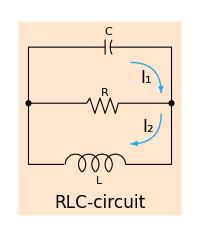

```mathematica
Graphics[{{LightOrange,Rectangle[{1.2,0.2},{2.8,2.1}]},(*{LightGray,Table[{Line[{{1.2,n},{3,n}}]},{n,0,2.2,0.1}]},{LightGray,Table[{Line[{{n,0},{n,2.2}}]},{n,1.2,3,0.1}]},*){Thickness[0.004],Line[{{1.3,1.3},{1.3,0.7},{1.65,0.7}}]},{Thickness[0.004],Circle[{1.76,0.7},0.1,{-0.85,π}]},{Thickness[0.004],Circle[{1.89,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.02,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.15,0.7},0.1,{0,π+0.85}]},{Thickness[0.004],Line[{{2.25,0.7},{2.7,0.7},{2.7,1.3}}]},{Thickness[0.004],Circle[{2.25,1.85},0.15,{π-0.5,π+0.5}]},{Thickness[0.004],Line[{{2.7,1.3},{2.7,1.85},{2.1,1.85}}]},{Thickness[0.004],Line[{{2.05,1.85},{1.3,1.85},{1.3,1.3}}]},{Disk[{1.3,1.3},0.03]},{Disk[{2.7,1.3},0.03]},{Text[Style["R",Medium],{2.05,1.4}]},{Text[Style["L",Medium],{1.99,0.54}]},{Text[Style["RLC-circuit",17],{2,0.32}]},{Text[Style["C",Medium],{2.08,2}]},{Thickness[0.004],Line[{{1.3,1.3},{1.87,1.3},{1.9,1.35},{1.95,1.2},{2,1.35},{2.05,1.2},{2.1,1.35},{2.15,1.2},{2.18,1.3},{2.7,1.3}}]},{Thickness[0.004],Line[{{2.05,1.775},{2.05,1.925}}]},{RGBColor[0.113,0.686,0.925],Arrow[BezierCurve[{{2.6,1.2},{2.6,0.9},{2.3,0.9}}]]},{RGBColor[0.113,0.686,0.925],Arrow[BezierCurve[{{2.3,1.7},{2.6,1.7},{2.6,1.4}}]]},{Text[Style["I_1",17],{2.45,1.55}]},{Text[Style["I_2",17],{2.47,1.07}]}},(*Axes->True,*)ImageSize->200(*,Ticks->{Range[0,3,0.1],Range[0,2.2,0.1]}*)]
```